# Figure 4 (ASER)

Clicking Run all evaluates the whole notebook from top to bottom . Some computations may take a while, so please wait until all cells have finished running .

```mathematica
Button["Run all",
With[{nb=ButtonNotebook[]},
FrontEndTokenExecute[nb,"EvaluateNotebook"];
SelectionMove[nb,After,Notebook]
]
]
```

Run all

#### Sum inid prods_ inid M=5.

```mathematica
ClearAll["Global`*"];
M=5;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4];
R1=∑_(j=1)^M ER[j,1];
f[G_,M_,γ_,α1_,μ1_,Ω1_]:=1/(2 √π)∑_(i=0)^500 ((-1)^i (√(G/M γ))^(-α1 (i+μ1)) μ1^(i+μ1) Ω1^(-α1 (i+μ1)) Gamma[1/2 (1+i α1+α1 μ1)])/(i!(i+μ1) Gamma[μ1]);

h[G_,M_,γ_,α1_,μ1_,Ω1_]:=(α1 μ1^μ1)/(2 Ω1^(μ1 α1)Gamma[μ1])NIntegrate[r^(α1 μ1-1)Exp[-μ1 (r/Ω1)^α1]Erfc[r √(G/M γ)],{r,0,∞}];
g[G_,M_,γ_,α1_,μ1_,Ω1_]:=1/(2 √π) ((√(G/M γ))^(-α1 (μ1))μ1^μ1 Ω1^(-α1 (μ1)) Gamma[1/2 (1+α1 μ1)])/(μ1 Gamma[μ1]);
```

```mathematica
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]]);
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
r=1;
(*β=Ω1^2/μ1^(2/α1)γ;*)
LB=-25;
UB=15;
Δ=1;
γdb=Table[10^(i/10),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T1=Table[{γs[[j]],h[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb]}];
T1S=Table[{γs[[j]],h[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb],3}];
T1A=Table[{γs[[j]],g[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb]}];
```

#### M=6

```mathematica
M=6;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};
ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5];
R1=∑_(j=1)^M ER[j,1];
h[G_,M_,γ_,α1_,μ1_,Ω1_]:=(α1 μ1^μ1)/(2 Ω1^(μ1 α1)Gamma[μ1])NIntegrate[r^(α1 μ1-1)Exp[-μ1 (r/Ω1)^α1]Erfc[r √(G/M γ)],{r,0,∞}];
g[G_,M_,γ_,α1_,μ1_,Ω1_]:=1/(2 √π) ((√(G/M γ))^(-α1 (μ1))μ1^μ1 Ω1^(-α1 (μ1)) Gamma[1/2 (1+α1 μ1)])/(μ1 Gamma[μ1]);
```

```mathematica
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]]);
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
LB=-25;
UB=15;
Δ=1;
γdb=Table[10^(i/10),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T2=Table[{γs[[j]],h[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb]}];
T2S=Table[{γs[[j]],h[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb],3}];
T2A=Table[{γs[[j]],g[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb]}];
```

#### Sum inid prods_ inid M=7.

```mathematica
M=7;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};
Subscript[mv, 7]={34/10,36/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};
Subscript[ov, 7]={44/10,46/10};
ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6];
R1=∑_(j=1)^M ER[j,1];
h[G_,M_,γ_,α1_,μ1_,Ω1_]:=(α1 μ1^μ1)/(2 Ω1^(μ1 α1)Gamma[μ1])NIntegrate[r^(α1 μ1-1)Exp[-μ1 (r/Ω1)^α1]Erfc[r √(G/M γ)],{r,0,∞}];
g[G_,M_,γ_,α1_,μ1_,Ω1_]:=1/(2 √π) ((√(G/M γ))^(-α1 (μ1))μ1^μ1 Ω1^(-α1 (μ1)) Gamma[1/2 (1+α1 μ1)])/(μ1 Gamma[μ1]);
```

```mathematica
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]]);
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
LB=-25;
UB=15;
Δ=1;
γdb=Table[10^(i/10),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T3=Table[{γs[[j]],h[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb]}];
T3S=Table[{γs[[j]],h[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb],3}];
T3A=Table[{γs[[j]],g[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb]}];
```

#### Sum inid prods_ inid M=8.

```mathematica
M=8;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};
Subscript[mv, 7]={34/10,36/10};
Subscript[mv, 8]={38/10,40/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};
Subscript[ov, 7]={44/10,46/10};
Subscript[ov, 8]={48/10,50/10};
ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7];
R1=∑_(j=1)^M ER[j,1];
h[G_,M_,γ_,α1_,μ1_,Ω1_]:=(α1 μ1^μ1)/(2 Ω1^(μ1 α1)Gamma[μ1])NIntegrate[r^(α1 μ1-1)Exp[-μ1 (r/Ω1)^α1]Erfc[r √(G/M γ)],{r,0,∞}];
g[G_,M_,γ_,α1_,μ1_,Ω1_]:=1/(2 √π) ((√(G/M γ))^(-α1 (μ1))μ1^μ1 Ω1^(-α1 (μ1)) Gamma[1/2 (1+α1 μ1)])/(μ1 Gamma[μ1]);
```

```mathematica
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]]);
μ1=Sol[[1,2]];
α1=Sol[[2,2]];

LB=-25;
UB=15;
Δ=1;
γdb=Table[10^(i/10),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T4=Table[{γs[[j]],h[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb]}];
T4S=Table[{γs[[j]],h[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb],3}];
T4A=Table[{γs[[j]],g[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb]}];
```

#### Sum inid prods_ inid M=9.

```mathematica
M=9;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};
Subscript[mv, 7]={34/10,36/10};
Subscript[mv, 8]={38/10,40/10};
Subscript[mv, 9]={42/10,44/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};
Subscript[ov, 7]={44/10,46/10};
Subscript[ov, 8]={48/10,50/10};
Subscript[ov, 9]={52/10,54/10};
ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7-n8]ER[9,n8];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7-n8]ER[9,n8];
R1=∑_(j=1)^M ER[j,1];
h[G_,M_,γ_,α1_,μ1_,Ω1_]:=(α1 μ1^μ1)/(2 Ω1^(μ1 α1)Gamma[μ1])NIntegrate[r^(α1 μ1-1)Exp[-μ1 (r/Ω1)^α1]Erfc[r √(G/M γ)],{r,0,∞}];
g[G_,M_,γ_,α1_,μ1_,Ω1_]:=1/(2 √π) ((√(G/M γ))^(-α1 (μ1))μ1^μ1 Ω1^(-α1 (μ1)) Gamma[1/2 (1+α1 μ1)])/(μ1 Gamma[μ1]);
```

```mathematica
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]]);
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
LB=-25;
UB=15;
Δ=1;
γdb=Table[10^(i/10),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T5=Table[{γs[[j]],h[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb]}];
T5S=Table[{γs[[j]],h[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb],3}];
T5A=Table[{γs[[j]],g[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb]}];
```

#### Sum inid prods_ inid M=10.

```mathematica
M=10;
Subscript[mv, 1]={10/10,12/10};
Subscript[mv, 2]={14/10,16/10};
Subscript[mv, 3]={18/10,20/10};
Subscript[mv, 4]={22/10,24/10};
Subscript[mv, 5]={26/10,28/10};
Subscript[mv, 6]={30/10,32/10};
Subscript[mv, 7]={34/10,36/10};
Subscript[mv, 8]={38/10,40/10};
Subscript[mv, 9]={42/10,44/10};
Subscript[mv, 10]={46/10,48/10};
Subscript[ov, 1]={2,22/10};
Subscript[ov, 2]={24/10,26/10};
Subscript[ov, 3]={28/10,30/10};
Subscript[ov, 4]={32/10,34/10};
Subscript[ov, 5]={36/10,38/10};
Subscript[ov, 6]={40/10,42/10};
Subscript[ov, 7]={44/10,46/10};
Subscript[ov, 8]={48/10,50/10};
Subscript[ov, 9]={52/10,54/10};
Subscript[ov, 10]={56/10,58/10};
ER[i_,n_]:=Module[{m},
m=Subscript[mv, i];
Ωr=Subscript[ov, i];
S=∏_(j=1)^2 (Gamma[m[[j]]+n/2]/Gamma[m[[j]]](Ωr[[j]]/m[[j]])^(n/2));
S
];
n=2;
R2=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 ∑_(n9=0)^n8 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]Binomial[n8,n9]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7-n8]ER[9,n8-n9]ER[10,n9];
n=4;
R4=∑_(n1=0)^n ∑_(n2=0)^n1 ∑_(n3=0)^n2 ∑_(n4=0)^n3 ∑_(n5=0)^n4 ∑_(n6=0)^n5 ∑_(n7=0)^n6 ∑_(n8=0)^n7 ∑_(n9=0)^n8 Binomial[n,n1]Binomial[n1,n2]Binomial[n2,n3]Binomial[n3,n4]Binomial[n4,n5]Binomial[n5,n6]Binomial[n6,n7]Binomial[n7,n8]Binomial[n8,n9]ER[1,n-n1]ER[2,n1-n2]ER[3,n2-n3]ER[4,n3-n4]ER[5,n4-n5]ER[6,n5-n6]ER[7,n6-n7]ER[8,n7-n8]ER[9,n8-n9]ER[10,n9];
R1=∑_(j=1)^M ER[j,1];
h[G_,M_,γ_,α1_,μ1_,Ω1_]:=(α1 μ1^μ1)/(2 Ω1^(μ1 α1)Gamma[μ1])NIntegrate[r^(α1 μ1-1)Exp[-μ1 (r/Ω1)^α1]Erfc[r √(G/M γ)],{r,0,∞}];
g[G_,M_,γ_,α1_,μ1_,Ω1_]:=1/(2 √π) ((√(G/M γ))^(-α1 (μ1))μ1^μ1 Ω1^(-α1 (μ1)) Gamma[1/2 (1+α1 μ1)])/(μ1 Gamma[μ1]);
```

```mathematica
Sol=FindRoot[{Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==(R1)^2/((R2)-(R1)^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==(R2)^2/((R4)-(R2)^2)},{{μ,1},{α,1}}];
Ω1=((Sol[[1,2]]^(1/Sol[[2,2]])Gamma[Sol[[1,2]]](R1))/Gamma[Sol[[1,2]]+1/Sol[[2,2]]]);
μ1=Sol[[1,2]];
α1=Sol[[2,2]];
LB=-25;
UB=15;
Δ=1;
γdb=Table[10^(i/10),{i,LB,UB,Δ}];
γs=Table[i,{i,LB,UB,Δ}];
T6=Table[{γs[[j]],h[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb]}];
T6S=Table[{γs[[j]],h[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb],3}];
T6A=Table[{γs[[j]],g[1,M,γdb[[j]],N[α1,100],N[μ1,100],N[Ω1,100]]},{j,1,Length[γdb]}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(*The following data was obtained with the file MonteCarlo-OP-ASER.nb*)
{T1S,T2S,T3S,T4S,T5S,T6S}={{{-24.999999999999996,0.326807`600.},{-22.999999999999996,0.286754`600.},{-20.999999999999996,0.240853`600.},{-18.999999999999996,0.18988`600.},{-16.999999999999996,0.137475`600.},{-14.999999999999996,0.088962`600.},{-12.999999999999998,0.049313`600.},{-10.999999999999998,0.022587`600.},{-9.,0.008131`600.},{-7.,0.002263`600.},{-5.,0.000473`600.},{-3.,0.000078`600.},{-1.,9.`600.*^-6},{1.,1.`600.*^-6},{3.,0},{5.,0},{7.,0},{9.,0},{10.999999999999998,0},{12.999999999999998,0},{14.999999999999996,0},{16.999999999999996,0},{18.999999999999996,0}},{{-24.999999999999996,0.297638`600.},{-22.999999999999996,0.252682`600.},{-20.999999999999996,0.202064`600.},{-18.999999999999996,0.149269`600.},{-16.999999999999996,0.098136`600.},{-14.999999999999996,0.055577`600.},{-12.999999999999998,0.025545`600.},{-10.999999999999998,0.009025`600.},{-9.,0.002316`600.},{-7.,0.000412`600.},{-5.,0.000053`600.},{-3.,5.`600.*^-6},{-1.,0},{1.,0},{3.,0},{5.,0},{7.,0},{9.,0},{10.999999999999998,0},{12.999999999999998,0},{14.999999999999996,0},{16.999999999999996,0},{18.999999999999996,0}},{{-24.999999999999996,0.268796`600.},{-22.999999999999996,0.219791`600.},{-20.999999999999996,0.166853`600.},{-18.999999999999996,0.113661`600.},{-16.999999999999996,0.066962`600.},{-14.999999999999996,0.032047`600.},{-12.999999999999998,0.011844`600.},{-10.999999999999998,0.003059`600.},{-9.,0.000543`600.},{-7.,0.000062`600.},{-5.,3.`600.*^-6},{-3.,0},{-1.,0},{1.,0},{3.,0},{5.,0},{7.,0},{9.,0},{10.999999999999998,0},{12.999999999999998,0},{14.999999999999996,0},{16.999999999999996,0},{18.999999999999996,0}},{{-24.999999999999996,0.240565`600.},{-22.999999999999996,0.188332`600.},{-20.999999999999996,0.134691`600.},{-18.999999999999996,0.083981`600.},{-16.999999999999996,0.043438`600.},{-14.999999999999996,0.017516`600.},{-12.999999999999998,0.0049`600.},{-10.999999999999998,0.000975`600.},{-9.,0.000116`600.},{-7.,5.`600.*^-6},{-5.,0},{-3.,0},{-1.,0},{1.,0},{3.,0},{5.,0},{7.,0},{9.,0},{10.999999999999998,0},{12.999999999999998,0},{14.999999999999996,0},{16.999999999999996,0},{18.999999999999996,0}},{{-24.999999999999996,0.21306`600.},{-22.999999999999996,0.159035`600.},{-20.999999999999996,0.106004`600.},{-18.999999999999996,0.059858`600.},{-16.999999999999996,0.026864`600.},{-14.999999999999996,0.008599`600.},{-12.999999999999998,0.001839`600.},{-10.999999999999998,0.000207`600.},{-9.,0.000014`600.},{-7.,0},{-5.,0},{-3.,0},{-1.,0},{1.,0},{3.,0},{5.,0},{7.,0},{9.,0},{10.999999999999998,0},{12.999999999999998,0},{14.999999999999996,0},{16.999999999999996,0},{18.999999999999996,0}},{{-24.999999999999996,0.187012`600.},{-22.999999999999996,0.132375`600.},{-20.999999999999996,0.081597`600.},{-18.999999999999996,0.041305`600.},{-16.999999999999996,0.015669`600.},{-14.999999999999996,0.003998`600.},{-12.999999999999998,0.000618`600.},{-10.999999999999998,0.000043`600.},{-9.,1.`600.*^-6},{-7.,0},{-5.,0},{-3.,0},{-1.,0},{1.,0},{3.,0},{5.,0},{7.,0},{9.,0},{10.999999999999998,0},{12.999999999999998,0},{14.999999999999996,0},{16.999999999999996,0},{18.999999999999996,0}}};
```

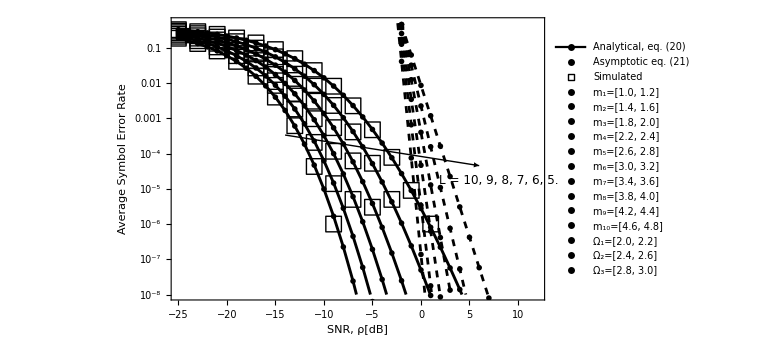

```mathematica
F1=ListLogPlot[{T1,T2,T3,T4,T5,T6,T1S,T2S,T3S,T4S,T5S,T6S,T1A,T2A,T3A,T4A,T5A,T6A},PlotStyle->{{Black,Thickness[0.0036]},{Black,Thickness[0.0036]},{Black,Thickness[0.0036]},{Black,Thickness[0.0036]},{Black,Thickness[0.0036]},{Black,Thickness[0.0036]},Black,Black,Black,Black,Black,Black,{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed}},Joined->{True,True,True,True,True,True,False,False,False,False,False,False,True,True,True,True,True,True},PlotMarkers->{{"",16},{"",16},{"",16},{"",16},{"",16},{"",16},{" □",16},{" □",16},{" □",16},{" □",16},{" □",16},{" □",16}},GridLines->Automatic,GridLinesStyle->Directive[White,Dashed,Thin],Frame-> True,FrameStyle->Directive[Black,18,FontFamily-> "Helvetica"],FrameLabel->{"SNR, ρ[dB]","Average Symbol Error Rate"},ImageSize->Large,PlotRange->{{-25,12},{10^-8,1/2}},Axes->False,Epilog->{Text[Style["L = 10, 9, 8, 7, 6, 5.",12],{8,-11}],{Arrowheads[Medium],Black,Arrow[{{-14,-8},{6,-10}}]}},PlotLegends->{Placed[LineLegend[{Black,Black,Black},{"Analytical, eq. (20)","Asymptotic eq. (21)","Simulated"},Joined->{True,False,False},LegendMarkers->{{"",16},{"--",16},{"□",16}},LabelStyle->{Black,14,FontFamily-> "Helvetica"}],{0.85,0.86}],Placed[LineLegend[{Black,Black,Black,Black,Black,Black,Black,Black,Black,Black,Black},{"m_1=[1.0, 1.2]","m_2=[1.4, 1.6]","m_3=[1.8, 2.0]","m_4=[2.2, 2.4]","m_5=[2.6, 2.8]","m_6=[3.0, 3.2]","m_7=[3.4, 3.6]","m_8=[3.8, 4.0]","m_9=[4.2, 4.4]","m_10=[4.6, 4.8]"},Joined->{False,False,False,False,False,False,False,False,False,False},LegendMarkers->{{"",14},{"",16}},LabelStyle->{Black,9,FontFamily-> "Helvetica"}],{0.06,0.37}],Placed[LineLegend[{Black,Black,Black,Black,Black,Black,Black,Black,Black,Black,Black},{"Ω_1=[2.0, 2.2]","Ω_2=[2.4, 2.6]","Ω_3=[2.8, 3.0]","Ω_4=[3.2, 3.4]","Ω_5=[3.6, 3.8]","Ω_6=[4.0, 4.2]","Ω_7=[4.4, 4.6]","Ω_8=[4.8, 5.0]","Ω_9=[5.2, 5.4]","Ω_10=[5.6, 5.8]"},Joined->{False,False,False,False,False,False,False,False,False,False},LegendMarkers->{{"",14},{"",16}},LabelStyle->{Black,9,FontFamily-> "Helvetica"}],{0.19,0.37}]},FrameTicks->{{{{1,"1"},{0.1,"10^-1"},{0.01,"10^-2"},{10^-3,"10^-3"},{10^-4,"10^-4"},{10^-5,"10^-5"},{10^-6,"10^-6"},{10^-7,"10^-7"},{10^-8,"10^-8"}},None},{Automatic,None}}]
```